Radiation pressure for degenerate internal squeezing
Using radiation pressure term from Hamiltonian in Li et al, 2020

```mathematica
(*unifying symbols: SRC mode is now b, losses are now γ*)
(*β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=αGW^2/(2^(1/2)ℏ μ);*)
(*
Ra=((1-Rpd)^(1/2)2ⅈ ωs (γR γa)^(1/2)Γ. invMb.invMa.Inverse[Γ].({{1, 0}, {0, -1}}))//Simplify;
T=((1-Rpd)^(1/2)ωs β(2 γR)^(1/2)Γ. invMb.invMa)//Simplify;
*)
(*changing ωs to ⅈ ωs and ϕ to π/2 in Hamiltonian, preserves sign of χ for squeezing*)
(*setting global assumptions*)
$Assumptions={Ω>0,γa≥0,γbtot≥γR>0,1>Rpd≥0,χ≥0,ωs>0,Element[β,Reals],ρRP≥0};

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mb=(γbtot-ⅈ Ω)Id-χ({{0, 1}, {1, 0}})+ωs^2 Inverse[Ma];(*ϕ to π/2 in Hamiltonian*)
invMb=Inverse[Mb]//Simplify;

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ])//Simplify;
Ra=(-(1-Rpd)^(1/2)2 ωs(γR γa)^(1/2)Γ. invMb.invMa.Inverse[Γ])//Simplify;(*ωs to ⅈ ωs in Hamiltonian*)
Rb=(-(1-Rpd)^(1/2)2( γR(γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ])//Simplify;
T=(-(1-Rpd)^(1/2)ωs (-ⅈ β)(2 γR)^(1/2)Γ. invMb.invMa.({{1, 0}, {0, -1}}))//Simplify;(*ωs to ⅈ ωs in Hamiltonian*)
Sx=Simplify[(
Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rpd Id),TimeConstraint->{1,10}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,10}];(*2nd index: [[1]] to remove atomic brackets {...}*)
sigTransferAbs=ComplexExpand[Abs[sigTransfer]]//Simplify;
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,10}];
```

```mathematica
(*signal transfer function -- demonstration of factor of two*)
FullSimplify[(T.({{1}, {1}}))[[2]][[1]]/.{ρRP->0,Rpd->0,γa->0,γbtot->γR,β->-β}];
FullSimplify[(T.ConjugateTranspose[T])[[2,2]]/.{ρRP->0,Rpd->0,γa->0,γbtot->γR,β->-β}];
Print["sig. transfer fn.: ",Simplify[ComplexExpand[Abs[%%]^2]]," vs ", %]
```

sig. transfer fn.: (4 β^2 γR ωs^2)/((γR+χ)^2 Ω^2+(Ω^2-ωs^2)^2) vs (2 β^2 γR ωs^2)/((γR+χ)^2 Ω^2+Ω^4-2 Ω^2 ωs^2+ωs^4)

```mathematica
(*with RP off, does it reduce to (ASD)^2 from degIntSqz.nb?*)
PSDShdegIntSqz=1/(4 γR ωs^2 β^2)((((2γR-γbtot-χ)γa+Ω^2-ωs^2)^2
						+Ω^2(γa-(2γR-γbtot-χ))^2)
+(γa^2+ Ω^2)4γR (γbtot-γR)
+4γR γa ωs^2
+ Rpd/(1-Rpd)(((-γbtot-χ)γa+Ω^2-ωs^2)^2
		+Ω^2(γa-(-γbtot-χ))^2));
Print["Rad. pressure off, does it reduce to degIntSqz?: ",(%==(Sh/.{ρRP->0,β->-β}))//ComplexExpand//Simplify]
```

Rad. pressure off, does it reduce to degIntSqz?: True

```mathematica
Collect[ComplexExpand[Sx[[2,2]]],{ρRP},Simplify]
```

(γbtot^2 Ω^2+2 γbtot χ Ω^2-4 γR χ Ω^2+4 Rpd γR χ Ω^2+χ^2 Ω^2+Ω^4+γa^2 (γbtot^2+2 γbtot χ+4 (-1+Rpd) γR χ+χ^2+Ω^2)+2 γa (γbtot+χ) ωs^2-2 Ω^2 ωs^2+ωs^4)/(γbtot^2 Ω^2+2 γbtot χ Ω^2+χ^2 Ω^2+Ω^4+γa^2 (γbtot^2+2 γbtot χ+χ^2+Ω^2)+2 γa (γbtot+χ) ωs^2-2 Ω^2 ωs^2+ωs^4)-(8 (-1+Rpd) γR ρRP^2 ωs^2 (γa (γbtot^2-2 γbtot χ+χ^2+Ω^2)+γbtot ωs^2))/(Ω^4 (γbtot^4 Ω^4+γa^4 (γbtot^4-2 γbtot^2 (χ^2-Ω^2)+(χ^2+Ω^2)^2)+4 γa^3 γbtot (γbtot^2-χ^2+Ω^2) ωs^2+2 γbtot^2 Ω^2 (-χ^2 Ω^2+(Ω^2-ωs^2)^2)+4 γa γbtot ωs^2 (γbtot^2 Ω^2-χ^2 Ω^2+(Ω^2-ωs^2)^2)+(χ^2 Ω^2+(Ω^2-ωs^2)^2)^2+2 γa^2 (γbtot^4 Ω^2+χ^4 Ω^2+(Ω^3-Ω ωs^2)^2+χ^2 (2 Ω^4-2 Ω^2 ωs^2-ωs^4)+γbtot^2 (-2 χ^2 Ω^2+2 Ω^4-2 Ω^2 ωs^2+3 ωs^4))))

```mathematica
(*stability is not the same: recognise denominator as the same as degIntSqz or the same * samewithχflip*)
((γbtot^2 Ω^2+2 γbtot χ Ω^2+χ^2 Ω^2+Ω^4+γa^2 (γbtot^2+2 γbtot χ+χ^2+Ω^2)+2 γa (γbtot+χ) ωs^2-2 Ω^2 ωs^2+ωs^4)==Abs[(γbtot+χ-I Ω)(γa-ⅈ Ω)+ωs^2]^2)//ComplexExpand//Simplify
((γbtot^4 Ω^4+γa^4 (γbtot^4-2 γbtot^2 (χ^2-Ω^2)+(χ^2+Ω^2)^2)+4 γa^3 γbtot (γbtot^2-χ^2+Ω^2) ωs^2+2 γbtot^2 Ω^2 (-χ^2 Ω^2+(Ω^2-ωs^2)^2)+4 γa γbtot ωs^2 (γbtot^2 Ω^2-χ^2 Ω^2+(Ω^2-ωs^2)^2)+(χ^2 Ω^2+(Ω^2-ωs^2)^2)^2+2 γa^2 (γbtot^4 Ω^2+χ^4 Ω^2+(Ω^3-Ω ωs^2)^2+χ^2 (2 Ω^4-2 Ω^2 ωs^2-ωs^4)+γbtot^2 (-2 χ^2 Ω^2+2 Ω^4-2 Ω^2 ωs^2+3 ωs^4)))==(Abs[(γbtot+χ-I Ω)(γa-ⅈ Ω)+ωs^2](Abs[(γbtot+χ-I Ω)(γa-ⅈ Ω)+ωs^2]/.χ->-χ))^2)//ComplexExpand//Simplify
```

True

True

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)

(*parameters from Korobko et al, 2019: benchmark 3rd generation detector*)
(*
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=20. 10^3(*m*);
Lsrc=56.(*m*);
Pcirc= 4. 10^6(*W*);
λ0=1550. 10^-9(*m*);
ω0=2π c/λ0;
Titm=0.07;
Tsrc=0.35;
ωs=c(Titm/(4 Lsrc Larm))^(1/2);
τRoundTripArm=(2 Larm)/c;
τRoundTripSRC=(2Lsrc)/c;
γR=-1/(2 τRoundTripSRC)Log[1-Tsrc];
*)

(*parameters for LIGO Voyager -- from sWLC model*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*W*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046;
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];


Print["ωs/γR=",ωs/γR]
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match
β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
M=200.(*kg*);
μ=M/4;
ρ=(2^(1/2)ℏ β^2)/(Larm^2 μ);
```

ωs/γR=10.

```mathematica
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
(*plotting sensitivity -- un-simplified Sh*)
(*taking real part to discard numerical error in tiny imaginary parts*)
QNwRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[Sx[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
sigwRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[sigTransferAbs]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
ASDShwRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[Sh]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
```

```mathematica
legendStyler[vals0_]:=(
If[Length[vals0]==4,vals=Join[vals0,{True}],vals=vals0];
paddedStrings=StringPadRight[{ToString[N[vals[[1]]/γR]],ToString[vals[[2]]],ToString[vals[[3]]],ToString[vals[[4]]]},4];
(*<> is StringJoin*)
Style[StringForm["χ/γR=``; T_(l, a)=``, T_(l, b)=``, R_PD=``"
<>If[Not[vals[[5]]],"; no RP",""],
paddedStrings[[1]],
paddedStrings[[2]],
paddedStrings[[3]],
paddedStrings[[4]]],
FontFamily->"Monospace"])

plotwRP[valsList_,plotLabel_:None,plotStyle_:{}]:=(
{fmin,fmax}={10^1,10^5};
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"degenerate internal squeezing\nparameters of LIGO Voyager",plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,PlotLegends->LineLegend[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{50,1}},PlotLegends->LineLegend[Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])
```

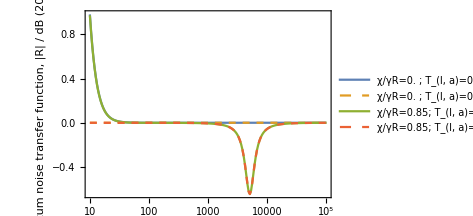
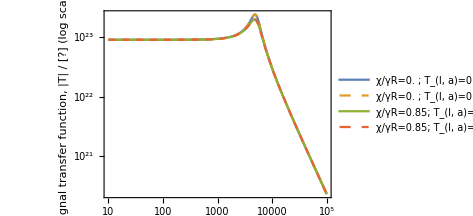
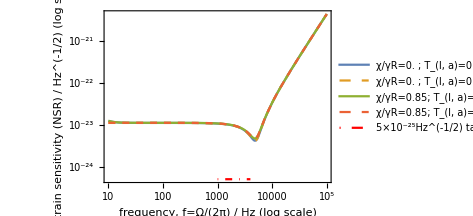

```mathematica
χRatio0=0.85;
loss0=0.1;
valsList1={
{0,loss0,loss0,loss0},
{0,loss0,loss0,loss0,False},
{χRatio0 γR,loss0,loss0,loss0},
{χRatio0 γR,loss0,loss0,loss0,False}};
plotwRP[valsList1,None,{,Dashed}]
(*NB: we don't see change at LF -- like Korobko suggests*)
```

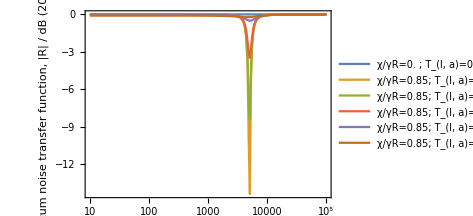
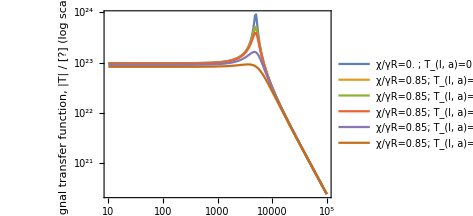
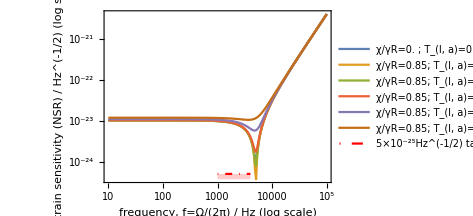

```mathematica
χRatio0=0.85;
valsList1={
{0,0,0,0,False},
{χRatio0 γR,0,0,0,False},
{χRatio0 γR,0.02,0,0,False},
{χRatio0 γR,0.1,0,0,False},
{χRatio0 γR,0.5,0,0,False},
{χRatio0 γR,0.8,0,0,False}};
plotwRP[valsList1]
```

```mathematica
(*NB: radiation pressure worsened because squeezing is in phase quadrature,
to-do: frequency dependent internal squeezing?*)
```

```mathematica
(*to-do: copy other plotting functions from degIntSqz:
NB: need to change parameters back to directly compare,
- stability --> changes, now becomes unstable on threshold -- why?,
- noise budget --> ,
- optimum sensitivity at probe frequency --> ,
*)
```

```mathematica
(*noise budget,
to-do: turn shot noise off to plot radiation pressure separately, how?*)
RpdwRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Rpd Id)[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
RinwRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Rin.ConjugateTranspose[Rin])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
RawRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Ra.ConjugateTranspose[Ra])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}
RbwRP[Ω0_,χ0_,Tla_,Tlb_,Rpd0_,ρRPTrue_:True]:=Re[Sqrt[(Rb.ConjugateTranspose[Rb])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0]}

plotNoiseBudgetwRP[params_,fRange_:{1,10^5}]:=
LogLinearPlot[{
20Log10[1],
20Log10[RinwRP@@Join[{2π f},params]],
20Log10[RawRP@@Join[{2π f},params]],
20Log10[RbwRP@@Join[{2π f},params]],
20Log10[RpdwRP@@Join[{2π f},params]],
20Log10[QNwRP@@Join[{2π f},params]]},{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_PD, PD loss","total quantum noise"},LabelStyle->Directive[10],LegendLabel->legendStyler[params]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2π) / Hz","degenerate internal squeezing\nparameters of LIGO Voyager"}},PerformanceGoal->"Speed"]
```

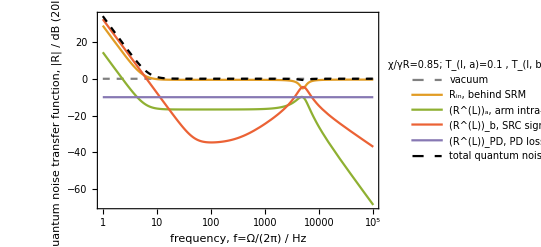

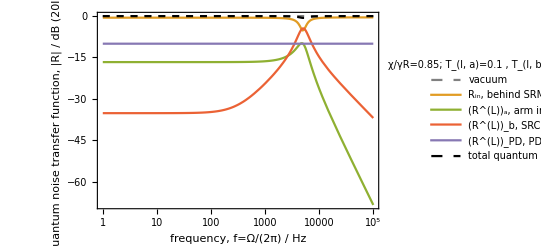

```mathematica
χRatio0=0.85;
plotNoiseBudgetwRP[{χRatio0 γR,0.1,0.1,0.1}]
plotNoiseBudgetwRP[{χRatio0 γR,0.1,0.1,0.1,False}]
```

```mathematica
(*optimum sensitivity at probe frequency*)
plotThresholdFinder[fProbe_,pastThreshold_:False,ρRPTrue_:True]:=(
probeNoiseRef=QNwRP[2π fProbe,0,0,0,0,ρRPTrue];(*reference has no γc loss*)
probeSigRef=sigwRP[2π fProbe,0,0,0,0,ρRPTrue];
probeSensRef=ASDShwRP[2π fProbe,0,0,0,0,ρRPTrue];
rpdList=Subdivide[0,0.5,5];
p1=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio γR,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio γR,0,0,rpdList[[i]],ρRPTrue]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["SNR (Hz^(1/2)) gain at `` kHz\nrelative to no loss/sqz. / dB (20 log_10(1/S_h))",N[fProbe/10^3]],},{,"degenerate internal squeezing\nparameters of LIGO Voyager"}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/γR∈(0,1), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10],LegendLabel->StringForm[If[Not[ρRPTrue],"no RP","with RP"],NumberForm[N[Tlc]]]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,AspectRatio->1,PerformanceGoal->"Speed"];
p2=ParametricPlot[{
{-20Log10[QNwRP[2π fProbe,1  γR,0,0,Rpd,ρRPTrue]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,1  γR,0,0,Rpd,ρRPTrue]/probeSensRef]}},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{StringForm["χ/γR=1, varying R_PD∈(``,``)",NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio  γR,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio  γR,0,0,rpdList[[i]],ρRPTrue]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/γR∈(1,2), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p1and2=Show[p1,p1b,p2];,
p1and2=Show[p1,p2];];
p3=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio  γR,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio  γR,0,0,rpdList[[i]],ρRPTrue]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["signal transfer function |T| at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",N[fProbe/10^3]],},{StringForm["quantum noise transfer function |R| at `` kHz\nrelative to no loss/sqz. / dB (-20 log_10)",N[fProbe/10^3]],}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{All,1}},ImageSize->350,AspectRatio->3/4,PerformanceGoal->"Speed"];
p4=ParametricPlot[
{-20Log10[QNwRP[2π fProbe,1  γR,0,0,Rpd,ρRPTrue]/probeNoiseRef],
20Log10[sigwRP[2π fProbe,1  γR,0,0,Rpd,ρRPTrue]/probeSigRef]},{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotRange->All,ImagePadding->{{80,10},{All,1}}];
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio  γR,0,0,rpdList[[i]],ρRPTrue]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio  γR,0,0,rpdList[[i]],ρRPTrue]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p3and4=Show[p3,p3b,p4];,
p3and4=Show[p3,p4];];
Column[{p1and2,p3and4},Spacings->0])
```

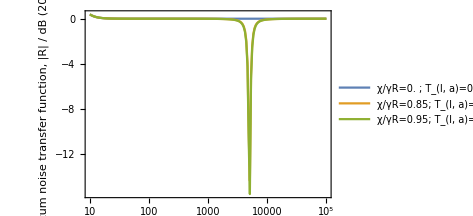
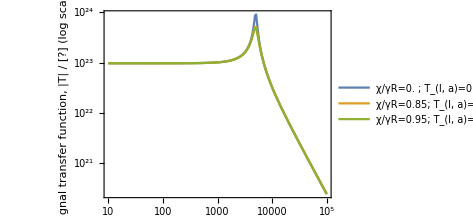
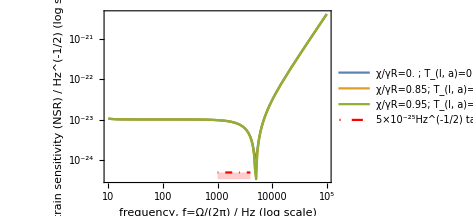

```mathematica
plotwRP[{
{0,0,0,0},
{0.85γR,0,0,0},
{0.95γR,0,0,0}}]
```

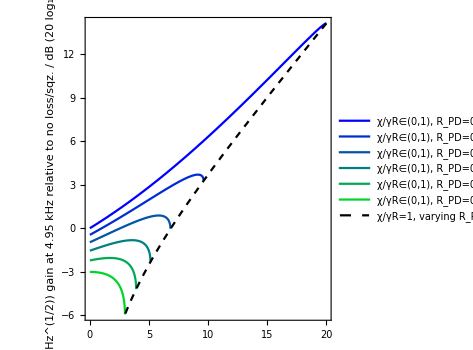
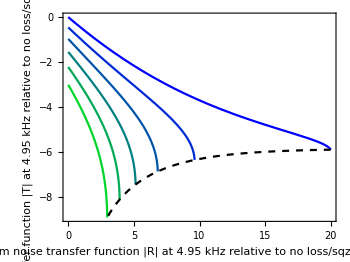

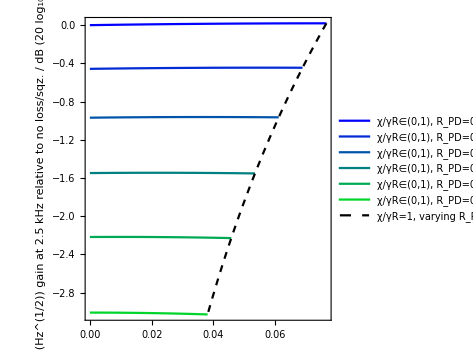
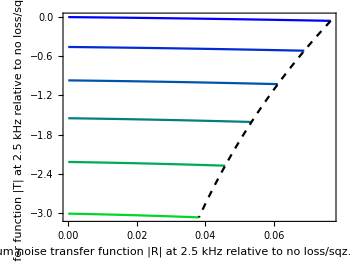

```mathematica
(*fProbe_,pastThreshold_:False,ρRPTrue_:True*)
plotThresholdFinder[0.99 ωs/(2π)(*Hz*)]
plotThresholdFinder[2500(*Hz*)]
(*LIGO Voyager parameters have short linewidth (γR) around ωs*)
```

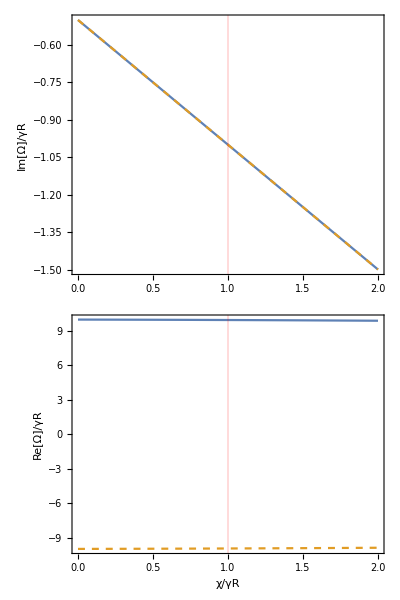
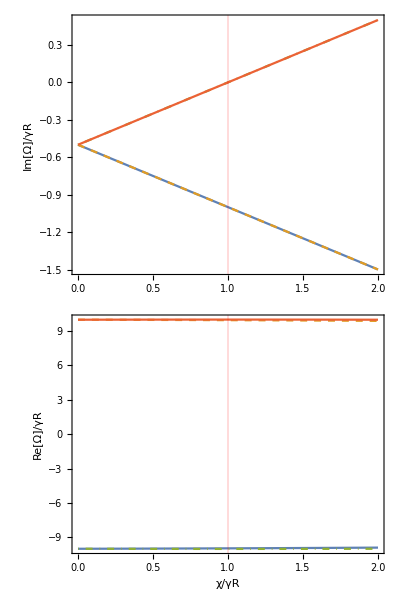

```mathematica
(*plotting stability*)
denom1[Tla_,Tlb_]:=γbtotFn[Tlb]+χ-I Ω+ωs^2/(γaFn[Tla]-ⅈ Ω);
denom2[Tla_,Tlb_]:=(γbtotFn[Tlb]+χ-I Ω+ωs^2/(γaFn[Tla]-ⅈ Ω))((γbtotFn[Tlb]+χ-I Ω+ωs^2/(γaFn[Tla]-ⅈ Ω))/.χ->-χ);
Clear[stabilitydISwRP]
stabilitydISwRP[Tla_,Tlb_]:=(
sol=NSolve[denom1[Tla,Tlb]==0,Ω];
p1=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,"poles of transfer function\nunstable when Im[Ω]≥0"}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
p2=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/γR",}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
sol=NSolve[denom2[Tla,Tlb]==0,Ω];
p12=Plot[Evaluate[Table[(Im[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{1,All}},ImageSize->300,Frame->True,FrameLabel->{{"Im[Ω]/γR",},{,"poles of transfer function\nunstable when Im[Ω]≥0"}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
p22=Plot[Evaluate[Table[(Re[Ω/.sol[[i]]]/.{χ->ratio γR})/γR,{i,1,Length[sol]}]],{ratio,0,2},PlotStyle->{,Dashed,DotDashed},
ImagePadding->{{50,2},{All,1}},ImageSize->300,Frame->True,FrameLabel->{{"Re[Ω]/γR",},{"χ/γR",}},GridLines->{{{1,Red}},None},PerformanceGoal->"Speed"];
Row[{Column[{p1,p2}],Column[{p12,p22}]}])

stabilitydISwRP[0,0]
```